```mathematica
(* *****************************************
The following is the mathematical construct of the transition matrix and the kappa scalar limits as defined, specified, discussed and illustrated within the article entitled "Quantum Double-field Game Theory Model"(DFGT), 
By: Philip B. Alipour and Dr. T. Aaron Gulliver at the UNiversity of Victoria, BC Canada 
***************************************** *) 
DateList[] (**This is the date signifying the updated caontent entry since April 2015 upon the Ph.D. candidacy exam of Philip B. Alipour**)

mat1={{1,0,1},{1,1,1},{1,-1,-1}} 
mat2={{1,0,1},{1,0,1},{1,0,-1}}
mat3=mat1.mat2 
mat2prime=(1/Sqrt[2]){{1,0,-1},{1,0,-1},{1,0,-1}}
Tr[(mat1. mat2)]
Det[(mat1. mat2)] 
TransProb = 2/3
MaxTransProb = 8/9
mat1.mat2 //MatrixForm
N[Abs[(TransProb/3)*mat1.mat2]] //MatrixForm
N[Abs[(TransProb/2)*mat1.mat2]] //MatrixForm
N[Tr[Abs[(TransProb/2)*mat1.mat2]] ]//MatrixForm
```

{2021,8,29,16,57,55.9174824}

{{1,0,1},{1,1,1},{1,-1,-1}}

{{1,0,1},{1,0,1},{1,0,-1}}

{{2,0,0},{3,0,1},{-1,0,1}}

{{1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2)}}

3

0

2/3

8/9

(2 | 0 | 0
3 | 0 | 1
-1 | 0 | 1)

(0.444444 | 0. | 0.
0.666667 | 0. | 0.222222
0.222222 | 0. | 0.222222)

(0.666667 | 0. | 0.
1. | 0. | 0.333333
0.333333 | 0. | 0.333333)

1.

```mathematica
({{2, 0, 0}, {3, 0, 1}, {-1, 0, 1}})

(* The following results represent the final proof example's discussion for different outcomes: pre and post-switch states *)
```

```mathematica
{{2,0,0},{3,0,1},{-1,0,1}}
mat3left={{2},{3},{-1}}
mat3right={{0},{1},{1}}
mat1middle1={{0},{0},{-1}}
mat1middle2={{0},{1},{0}}
mat2right = {{1},{1},{-1}}
N[Abs[(TransProb/3)*mat3left] ] //MatrixForm
N[Abs[(TransProb/3)*mat1middle1] ] //MatrixForm
N[Abs[(TransProb/2)*mat3right] ] //MatrixForm
N[Abs[(TransProb/2)*mat2right] ] //MatrixForm
N[Abs[(MaxTransProb/3)*mat3left] ] //MatrixForm
N[Abs[(MaxTransProb/3)*mat1middle1] ] //MatrixForm
N[Abs[(MaxTransProb/2)*mat3right] ] //MatrixForm
N[Abs[(MaxTransProb/2)*mat2right] ] //MatrixForm
N[Abs[(MaxTransProb/3)*mat1middle2] ] //MatrixForm
N[Abs[(MaxTransProb/2)*mat3right] ] //MatrixForm
N[Abs[(MaxTransProb/2)*mat2right] ] //MatrixForm
```

{{2,0,0},{3,0,1},{-1,0,1}}

{{2},{3},{-1}}

{{0},{1},{1}}

{{0},{0},{-1}}

{{0},{1},{0}}

{{1},{1},{-1}}

(0.444444
0.666667
0.222222)

(0.
0.
0.222222)

(0.
0.333333
0.333333)

(0.333333
0.333333
0.333333)

(0.592593
0.888889
0.296296)

(0.
0.
0.296296)

(0.
0.444444
0.444444)

(0.444444
0.444444
0.444444)

(0.
0.296296
0.)

(0.
0.444444
0.444444)

(0.444444
0.444444
0.444444)

```mathematica
{{2,0,0},{3,0,1},{-1,0,1}}

(* The folllowing denote possile norm arguments involving entanglement and its pobssible extraction from the denisty mtrix through the pre and post-switch states(operatons) *)
```

```mathematica
mat2 mat1 //MatrixForm
```

(1 | 0 | 1
1 | 0 | 1
1 | 0 | 1)

```mathematica
MatrixForm[KroneckerProduct[Sqrt[2]mat1,(mat1 . mat2)] ] //MatrixForm
```

(2 √2 | 0 | 0 | 0 | 0 | 0 | 2 √2 | 0 | 0
3 √2 | 0 | √2 | 0 | 0 | 0 | 3 √2 | 0 | √2
-√2 | 0 | √2 | 0 | 0 | 0 | -√2 | 0 | √2
2 √2 | 0 | 0 | 2 √2 | 0 | 0 | 2 √2 | 0 | 0
3 √2 | 0 | √2 | 3 √2 | 0 | √2 | 3 √2 | 0 | √2
-√2 | 0 | √2 | -√2 | 0 | √2 | -√2 | 0 | √2
2 √2 | 0 | 0 | -2 √2 | 0 | 0 | -2 √2 | 0 | 0
3 √2 | 0 | √2 | -3 √2 | 0 | -√2 | -3 √2 | 0 | -√2
-√2 | 0 | √2 | √2 | 0 | -√2 | √2 | 0 | -√2)

```mathematica
MatrixForm[KroneckerProduct[(mat1 . mat2), Sqrt[2]mat2] ] //MatrixForm
```

(2 √2 | 0 | 2 √2 | 0 | 0 | 0 | 0 | 0 | 0
2 √2 | 0 | 2 √2 | 0 | 0 | 0 | 0 | 0 | 0
2 √2 | 0 | -2 √2 | 0 | 0 | 0 | 0 | 0 | 0
3 √2 | 0 | 3 √2 | 0 | 0 | 0 | √2 | 0 | √2
3 √2 | 0 | 3 √2 | 0 | 0 | 0 | √2 | 0 | √2
3 √2 | 0 | -3 √2 | 0 | 0 | 0 | √2 | 0 | -√2
-√2 | 0 | -√2 | 0 | 0 | 0 | √2 | 0 | √2
-√2 | 0 | -√2 | 0 | 0 | 0 | √2 | 0 | √2
-√2 | 0 | √2 | 0 | 0 | 0 | √2 | 0 | -√2)

```mathematica
Norm[mat3, Infinity]
```

4

```mathematica
N[Abs[EuclideanDistance[(mat2. mat1),mat3]-N[EuclideanDistance[mat2,( mat1. mat2)]]  ]]
```

0.994918

```mathematica
N[Abs[EuclideanDistance[(mat2. mat1), mat2]]]  (**The result comforms to the norm given in the Remark section of te paper**)
```

4.

```mathematica
Dot[mat1,mat2]
```

{{2,0,0},{3,0,1},{-1,0,1}}

```mathematica
Dot[mat2,mat1]
```

{{2,-1,0},{2,-1,0},{0,1,2}}

```mathematica
KroneckerProduct[mat2, mat1]//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1
1 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | -1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1
1 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | -1
1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | -1
1 | 1 | 1 | 0 | 0 | 0 | -1 | -1 | -1
1 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | 1)

```mathematica
KroneckerProduct[mat1, mat2]//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | -1
1 | 0 | 1 | -1 | 0 | -1 | -1 | 0 | -1
1 | 0 | 1 | -1 | 0 | -1 | -1 | 0 | -1
1 | 0 | -1 | -1 | 0 | 1 | -1 | 0 | 1)

```mathematica
KroneckerProduct[(mat1. mat2), mat2*κ/Sqrt[2]]//MatrixForm
```

(√2 κ | 0 | √2 κ | 0 | 0 | 0 | 0 | 0 | 0
√2 κ | 0 | √2 κ | 0 | 0 | 0 | 0 | 0 | 0
√2 κ | 0 | -√2 κ | 0 | 0 | 0 | 0 | 0 | 0
(3 κ)/(√2) | 0 | (3 κ)/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | κ/(√2)
(3 κ)/(√2) | 0 | (3 κ)/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | κ/(√2)
(3 κ)/(√2) | 0 | -(3 κ)/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | -κ/(√2)
-κ/(√2) | 0 | -κ/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | κ/(√2)
-κ/(√2) | 0 | -κ/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | κ/(√2)
-κ/(√2) | 0 | κ/(√2) | 0 | 0 | 0 | κ/(√2) | 0 | -κ/(√2))

```mathematica
KroneckerProduct[mat1*κ/Sqrt[2],(mat1. mat2)]//MatrixForm
```

```mathematica
({{√2 κ, 0, 0, 0, 0, 0, √2 κ, 0, 0}, {(3 κ)/(√2), 0, κ/(√2), 0, 0, 0, (3 κ)/(√2), 0, κ/(√2)}, {-κ/(√2), 0, κ/(√2), 0, 0, 0, -κ/(√2), 0, κ/(√2)}, {√2 κ, 0, 0, √2 κ, 0, 0, √2 κ, 0, 0}, {(3 κ)/(√2), 0, κ/(√2), (3 κ)/(√2), 0, κ/(√2), (3 κ)/(√2), 0, κ/(√2)}, {-κ/(√2), 0, κ/(√2), -κ/(√2), 0, κ/(√2), -κ/(√2), 0, κ/(√2)}, {√2 κ, 0, 0, -√2 κ, 0, 0, -√2 κ, 0, 0}, {(3 κ)/(√2), 0, κ/(√2), -(3 κ)/(√2), 0, -κ/(√2), -(3 κ)/(√2), 0, -κ/(√2)}, {-κ/(√2), 0, κ/(√2), κ/(√2), 0, -κ/(√2), κ/(√2), 0, -κ/(√2)}})
(* Phse Transition plots *)
```

```mathematica
1/2N[EuclideanDistance[Tr[(mat1. mat2)],Tr[mat2]]-N[EuclideanDistance[Tr[mat1],Tr[(mat1. mat2)]]]  ]
```

0.5

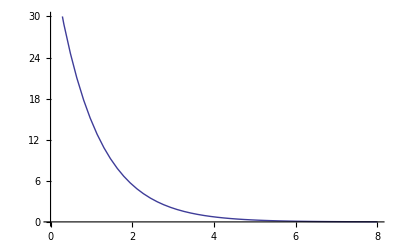
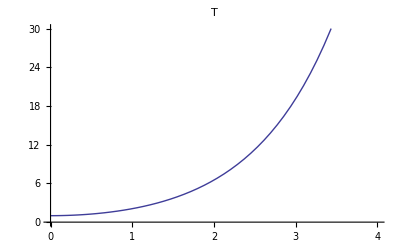
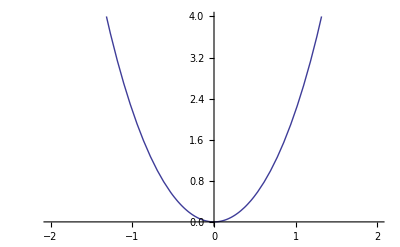
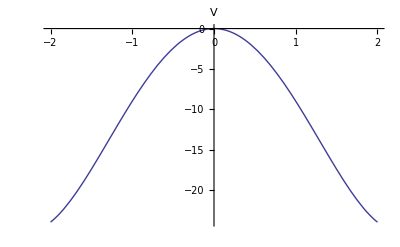
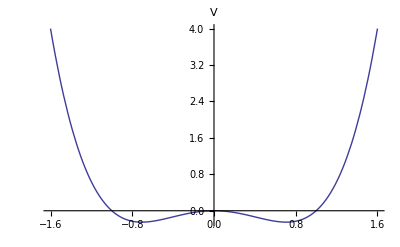

```mathematica
{Plot[-10x^2+x^4,{x,-2,2},PlotRange->{0,-40}, PlotLabel->"V"] Plot[x^4-x^2,{x,-2,2},PlotRange->{4,-4}, PlotLabel->"V"]
Plot[E^x+E^-x-1,{x,0,4},PlotRange->{0,30}, PlotLabel->"T"]Plot[(E^x+E^-x-2)*2,{x,-2,2},PlotRange->{0,4}]
Plot[40E^-x,{x,0,8},PlotRange->{0,30}]}
```

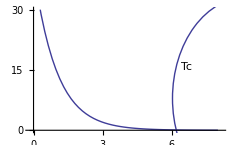

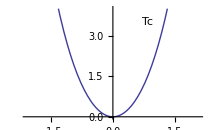
```mathematica
{-Graphics- -Graphics- -Graphics- -Graphics-}
```

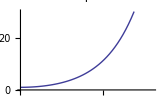
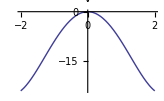
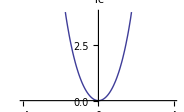
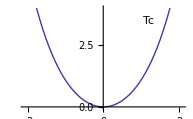
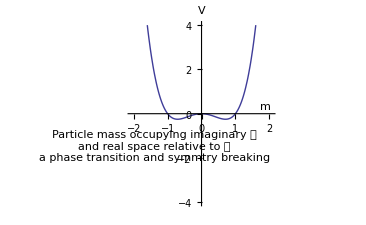

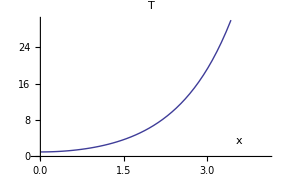

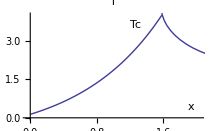

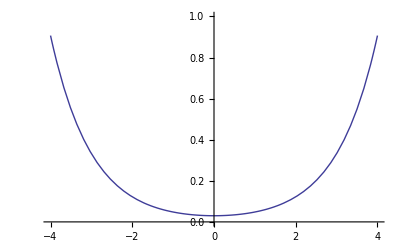

```mathematica
Plot[(5E^x+5E^-x-1)*0.01/3,{x,-4,4},PlotRange->{0,1}]
```

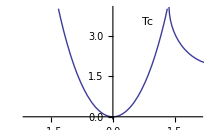

```mathematica
-Graphics-
(**The following plots display the limts of the kappa scalar relative to distance by order of magnitude **)
```

```mathematica
Plot3D[{X^(2*r)},{X,0,2},{r,-1,1}, AxesLabel->{Abs[κ],r, X},ColorFunction->"RustTones" ]
```

-Graphics3D-

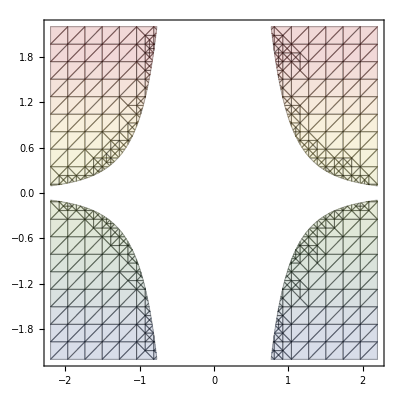

```mathematica
RegionPlot[2/(r^6 κ^2)≤2,{r,-2.2,2.2},{κ,-2.2,2.2},  PlotStyle->{Blue, Opacity[0.2]},Mesh -> All, ColorFunction->"DarkRainbow"]
```

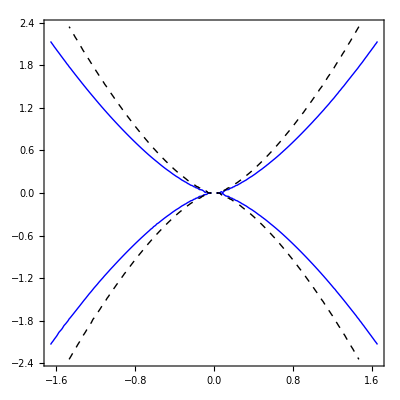

```mathematica
ContourPlot[{κ^4/r^6==1,κ^4/(3 r^6)==1},{r,-1.66,1.66},{κ,-2.34759,2.34759}, ContourStyle->{Blue,  Dashed }]
```